-1+(3+x) (3/2+(-1+(5/12-11/60 (-3+x)) (-1+x)) (1+x))

-1+(3+x) (3/2+(-1+(5/12-11/60 (-3+x)) (-1+x)) (1+x))

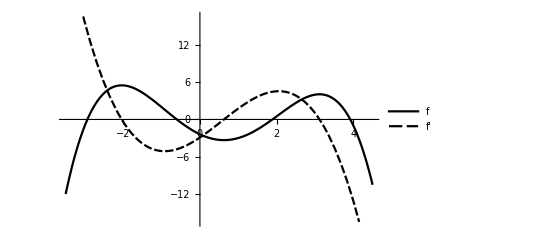

1/60 (-11 x^4+25 x^3+125 x^2-175 x-144)

```mathematica
p=InterpolatingPolynomial[{{-3,-1},{-1,2},{1,-3},{3,4},{4,-1}},x]
f[x_]=p/.x->x
Plot[{f[x],f'[x]},{x,-3.5,4.5},PlotLegends->{"f","f'"},PlotTheme->"Monochrome"]
f[x]//Simplify//TraditionalForm
```

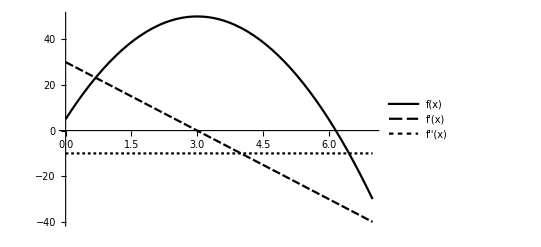

```mathematica
f[x_]:=5+30x-5x^2
Plot[{f[x],f'[x],f''[x]}, {x,0,7}, PlotTheme->"Monochrome",PlotLegends->"Expressions"]
```

```mathematica
f[x_]:=1/Sqrt[x]
```

```mathematica
f'[x]//Simplify
```

-1/(2 x^(3/2))